```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

```mathematica
GreedyRank[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeList[UndirectedGraph[{EdgeRules[Gout][[Rank[[i]]]]}]][[1]];
EdgeAssumption=Append[EdgeProcess,AddEdge];
If[Max[VertexDegree[EdgeAssumption]]≤ 2,
PartLoopAssumption=FindCycle[EdgeAssumption,Infinity,All];
If[PartLoopAssumption=={}||PartLoopAssumption≠{} && Length[VertexList[PartLoopAssumption[[1]]]]== Length[Pin],
EdgeProcess=EdgeAssumption;
If[PartLoopAssumption≠{} ,PartLoopProcess=PartLoopAssumption[[1]]],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
PartLoopProcess
)
(* RankからのGreedy *)
```

### 渦電流の計算

```mathematica
Pin={{5.05414,3.85871},{7.06428,3.28327},{2.61464,9.81381},{2.40214,8.56083},{5.23845,4.64195},{1.11492,9.10565},{6.31466,9.21289},{5.64583,3.23595},{6.44205,3.32215},{0.600516,0.656467},{3.18945,7.00796},{5.24422,4.64131},{5.16623,0.0434558},{8.4607,4.30481},{1.46913,6.19986},{4.69847,8.0504},{4.36569,8.49946},{1.15122,8.11397},{8.11883,7.35414},{5.00034,4.94393}}
(*Point input*)
```

{{5.05414,3.85871},{7.06428,3.28327},{2.61464,9.81381},{2.40214,8.56083},{5.23845,4.64195},{1.11492,9.10565},{6.31466,9.21289},{5.64583,3.23595},{6.44205,3.32215},{0.600516,0.656467},{3.18945,7.00796},{5.24422,4.64131},{5.16623,0.0434558},{8.4607,4.30481},{1.46913,6.19986},{4.69847,8.0504},{4.36569,8.49946},{1.15122,8.11397},{8.11883,7.35414},{5.00034,4.94393}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

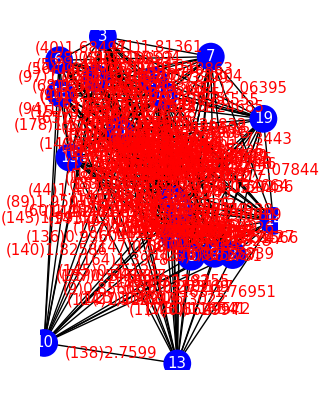

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### 解の構築

```mathematica
PDRank=Ordering[PD]
```

{77,85,162,181,26,113,4,11,7,97,19,38,68,56,25,116,73,8,40,31,61,127,74,124,150,151,149,178,67,108,109,1,135,51,52,129,29,22,152,66,65,111,37,50,154,45,94,90,118,174,184,76,146,117,156,185,79,96,13,81,158,183,128,175,182,187,10,177,176,95,180,41,30,49,12,103,186,190,161,82,84,159,57,80,157,36,15,14,134,70,112,115,155,78,138,18,16,104,72,123,55,62,169,120,126,153,189,131,119,86,110,171,33,106,83,160,28,163,3,121,54,9,6,132,140,114,99,107,130,17,39,46,69,172,34,101,148,24,100,53,71,91,75,137,145,58,32,125,2,5,59,122,179,136,27,188,21,133,164,98,147,42,170,64,87,143,43,35,88,168,20,165,48,60,173,23,141,89,166,139,142,93,63,167,105,44,92,144,47,102}

```mathematica
AbsCurr =Abs[Curr ];
```

```mathematica
CurrRank=Ordering[1/AbsCurr ](* 昇順 *)
```

{138,174,111,143,89,140,41,163,106,40,36,53,178,31,86,30,27,60,52,44,164,125,57,94,186,134,139,114,168,183,24,65,129,110,97,49,109,128,167,67,98,69,51,96,68,171,172,123,118,101,136,185,92,50,48,119,14,66,95,113,25,188,9,38,177,182,108,26,107,18,100,130,142,33,103,13,17,105,117,63,34,151,122,181,161,176,84,153,56,32,80,64,157,147,104,72,150,8,180,1,137,75,131,149,141,144,6,5,132,93,112,7,87,190,20,47,10,133,83,160,189,179,145,158,115,81,3,148,120,45,156,79,184,159,82,61,43,58,155,78,35,121,102,173,187,170,71,91,99,154,76,146,88,15,12,175,21,126,90,46,39,165,11,169,4,2,16,70,22,54,29,55,62,74,127,152,124,135,37,19,85,162,23,166,28,42,59,77,116,73}

```mathematica
PDCurrRank=Ordering[PD/AbsCurr](* 昇順 *)
```

{97,26,181,77,113,40,31,68,111,178,174,38,52,25,138,67,109,129,7,51,41,65,94,56,30,66,108,36,8,183,50,57,186,118,151,128,96,163,140,106,49,150,134,185,86,149,143,1,53,95,110,114,89,177,182,123,14,125,27,24,117,171,13,164,69,119,103,172,60,101,176,168,18,161,84,98,9,139,61,11,44,80,157,180,4,136,107,33,167,153,130,104,72,188,100,48,17,10,190,34,131,45,158,112,81,92,32,122,6,156,79,184,137,75,132,85,142,64,147,162,115,154,5,189,63,105,83,159,160,82,120,141,76,3,146,187,87,145,93,20,155,133,78,148,179,144,12,90,121,15,47,175,22,74,29,58,127,99,124,71,43,91,19,35,152,170,173,126,135,169,88,102,16,46,70,39,21,54,55,62,37,2,165,23,28,166,42,59,116,73}

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{8.78171,102.323,69.6397,1.36788,104.977,73.1574,1.63215,4.16644,72.4067,28.1812,1.44964,32.4437,23.706,41.961,40.8055,50.1995,80.8371,49.2762,2.28176,143.033,117.6,10.9243,154.833,88.4569,3.5481,0.935165,115.123,68.259,10.6731,31.1654,5.19055,99.0621,65.4593,85.1571,135.911,40.3703,14.0401,2.79592,81.7709,4.80967,30.7377,124.574,133.387,183.774,16.0391,82.396,200.951,147.,31.8457,14.7411,9.63358,10.0935,90.4316,71.0393,53.6972,3.35465,36.8883,97.2668,106.509,149.17,5.39726,54.2247,172.825,128.83,12.9471,11.7619,7.66158,3.05518,83.55,44.5338,91.7604,51.1856,3.95234,5.89447,93.5611,19.4055,0.00638592,47.8302,21.7069,38.3387,24.1567,35.5951,67.0359,36.0026,0.461475,62.4101,129.763,140.748,159.139,17.1115,92.4348,195.553,168.489,16.6856,29.8855,22.4863,1.98469,122.733,78.0015,89.6123,86.0249,205.78,32.8928,50.7085,180.201,66.4237,78.7417,7.96337,8.50932,63.8769,13.4699,45.1137,1.2814,77.064,45.9134,3.80021,20.6612,17.7647,60.9456,55.9372,70.4203,107.454,52.8403,6.20801,101.452,56.5311,5.70191,25.6827,10.3276,79.8629,59.4659,74.7473,119.922,43.2309,9.3308,112.485,94.2336,48.3702,164.647,75.749,158.082,166.169,131.609,199.365,95.222,19.7454,123.797,87.082,7.03246,6.41925,6.83821,11.363,57.3216,15.102,47.3647,21.0212,38.7995,24.5127,36.4036,67.6328,35.1779,0.505258,68.9452,121.363,145.975,160.533,174.873,141.919,55.4071,125.318,64.7679,84.4142,152.486,18.4106,26.0398,29.4036,28.8476,7.37326,110.011,30.358,0.782495,26.6086,25.1317,19.0387,21.3675,34.1388,27.4491,116.348,58.3417,34.6837}

```mathematica
PDWeightCurrRank=Ordering[PDWeight/AbsCurr ]
```

{77,181,26,113,97,68,40,38,31,7,25,178,56,111,67,52,109,8,129,51,174,108,65,151,150,4,11,94,66,149,85,50,1,162,41,118,138,183,61,96,30,185,128,186,36,57,49,117,134,95,182,13,177,106,163,86,140,14,176,103,123,110,45,180,161,84,114,53,171,80,19,157,119,143,18,10,184,81,158,156,24,125,154,79,69,27,127,74,190,172,89,101,9,164,104,72,153,33,124,76,112,60,146,107,98,131,168,130,29,136,22,17,100,139,187,82,159,44,34,115,90,188,6,167,132,48,152,189,32,135,122,75,137,175,83,160,120,155,12,78,92,147,3,64,5,15,142,63,105,145,148,87,121,141,133,179,37,20,93,99,58,144,126,71,91,70,47,169,16,43,35,170,55,46,39,62,173,54,88,21,102,2,165,116,73,23,28,166,42,59}

{37.6286,{1,20,5,12,9,2,14,19,7,16,17,11,4,3,6,18,15,10,13,8,1}}

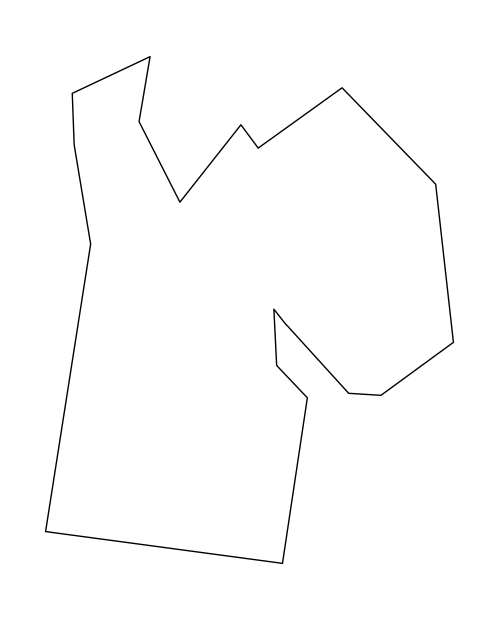

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
PartLoop1=GreedyRank[PDRank]
DelEdge
EdgeProcess
```

{5<->12,12<->1,1<->8,8<->9,9<->2,2<->14,14<->19,19<->7,7<->17,17<->16,16<->11,11<->15,15<->6,6<->18,18<->4,4<->3,3<->10,10<->13,13<->20,20<->5}

{20<->12,3<->6,17<->11}

{5<->12,20<->5,16<->17,9<->2,8<->9,1<->12,1<->8,6<->18,3<->4,4<->18,2<->14,16<->11,11<->15,7<->17,19<->7,6<->15,14<->19,10<->13,13<->20,3<->10}

{1,8,9,2,14,19,7,17,16,11,15,6,18,4,3,10,13,20,5,12,1}

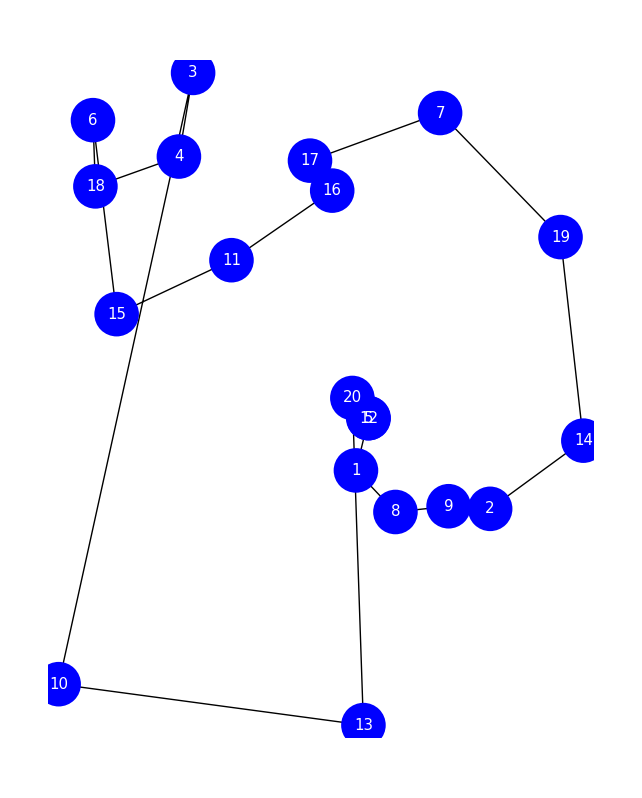

42.6422

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
PartLoop2=GreedyRank[CurrRank]
DelEdge
EdgeProcess
```

{10<->13,13<->14,14<->19,19<->7,7<->3,3<->6,6<->16,16<->2,2<->8,8<->9,9<->1,1<->12,12<->5,5<->20,20<->11,11<->17,17<->4,4<->15,15<->18,18<->10}

{6<->15,17<->6,9<->2,11<->1}

{10<->13,14<->19,19<->7,18<->10,7<->3,13<->14,3<->6,18<->15,4<->15,17<->4,16<->6,8<->9,8<->2,2<->16,17<->11,1<->9,11<->20,1<->12,20<->5,5<->12}

{1,12,5,20,11,17,4,15,18,10,13,14,19,7,3,6,16,2,8,9,1}

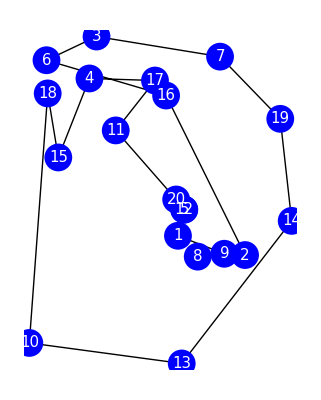

53.5869

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
PartLoop3=GreedyRank[PDCurrRank]
DelEdge
EdgeProcess
```

{6<->18,18<->4,4<->17,17<->16,16<->11,11<->15,15<->10,10<->13,13<->20,20<->5,5<->12,12<->1,1<->8,8<->9,9<->2,2<->14,14<->19,19<->7,7<->3,3<->6}

{3<->4}

{6<->18,9<->2,16<->17,5<->12,8<->9,3<->6,2<->14,4<->18,19<->7,14<->19,10<->13,17<->4,1<->8,7<->3,15<->10,16<->11,11<->15,1<->12,20<->5,13<->20}

{1,8,9,2,14,19,7,3,6,18,4,17,16,11,15,10,13,20,5,12,1}

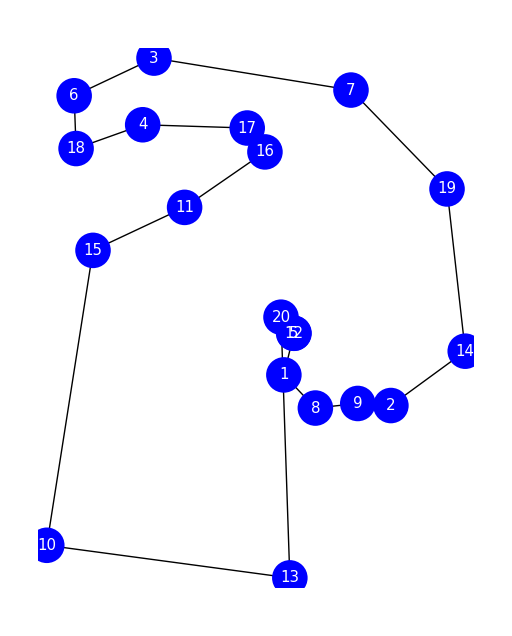

39.9749

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```

```mathematica
PartLoop4=GreedyRank[PDWeightCurrRank]
DelEdge
EdgeProcess
```

{5<->12,12<->20,20<->13,13<->10,10<->11,11<->15,15<->3,3<->6,6<->18,18<->4,4<->17,17<->16,16<->7,7<->19,19<->14,14<->2,2<->9,9<->8,8<->1,1<->5}

{3<->4,11<->20}

{5<->12,16<->17,9<->2,8<->9,6<->18,4<->18,3<->6,2<->14,1<->8,19<->7,17<->4,14<->19,7<->16,1<->5,11<->15,20<->12,10<->13,3<->15,11<->10,13<->20}

{1,5,12,20,13,10,11,15,3,6,18,4,17,16,7,19,14,2,9,8,1}

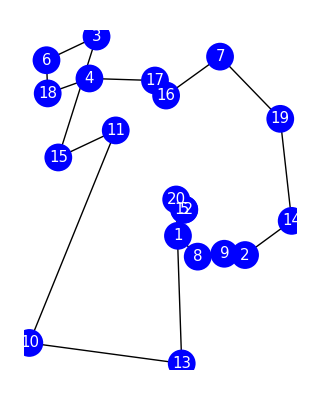

41.4255

```mathematica
VertexSortFromLoopEdgeList[PartLoop4]
Graphics[{line=Line[Pin[[%]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
ArcLength[line]//N
```